```mathematica
CrankNicolson[V_,ψ0_,L_,Ν_,T_,Δt_]:=
Block[{δ=L/(Ν-1.)},
Block[{H=SparseArray[{{n_,n_}->2./δ^2+V[-L/2+(n-1) δ],{n_,m_}/;Abs[n-m]==1->-1./δ^2},{Ν,Ν}],
ψ=Array[ψ0[-L/2+(#-1) δ]&,Ν]},
Block[{u=Inverse[IdentityMatrix[Ν]+I/2 Δt H].(IdentityMatrix[Ν]-I/2 Δt H)},
NestList[u.#&,ψ,T/Δt]
]
]
]
```

```mathematica
animate[V_,ψ0_,L_,Ν_,T_,Δt_]:=Module[{interpolation=ListInterpolation[Abs[CrankNicolson[V,ψ0,L,Ν,T,Δt]]^2,{{0,T},{-L/2,L/2}}]},
Animate[Plot[interpolation[t,x],{x,-L/2,L/2},PlotRange->{0,1}],{t,0,T}]
]
norm[V_,ψ0_,L_,Ν_,T_,Δt_]:=ListPlot[Total[Abs[#]^2] L/Ν&/@CrankNicolson[V,ψ0,L,Ν,T,Δt]]
energy[V_,ψ0_,L_,Ν_,T_,Δt_]:=Block[{δ=L/(Ν-1.)},
Block[{H=SparseArray[{{n_,n_}->2./δ^2+V[-L/2+(n-1) δ],{n_,m_}/;Abs[n-m]==1->-1./δ^2},{Ν,Ν}]},
ListPlot[Re[Conjugate[#].H.#]&/@CrankNicolson[V,ψ0,L,Ν,T,Δt]]
]
]
```

```mathematica
Timing[animate[0&,(Pi/2)^(-1/4) Exp[-#^2] Exp[I #]&,8,150,1/2,1/160]]
```

{0.173334,}

```mathematica
Timing[CrankNicolson[0&,(Pi/2)^(-1/4) Exp[-#^2] Exp[I #]&,8,150,1/2,1/160]][[1]]
```

0.083333

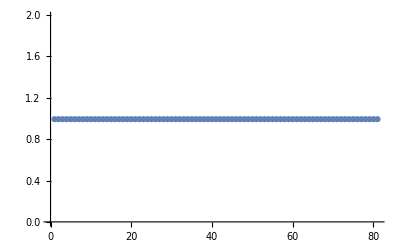

```mathematica
norm[0&,(Pi/2)^(-1/4) Exp[-#^2] Exp[I #]&,8,150,1/2,1/160]
```

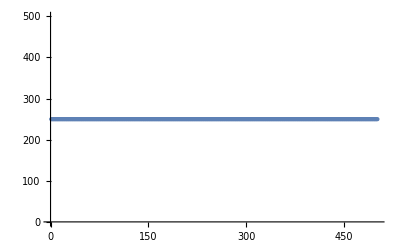

```mathematica
energy[0&,(Pi/2)^(-1/4) Exp[-#^2] Exp[I #]&,8,1000,1/2,1/1000]
```

```mathematica
animate[#^2&,1/(√8)(2 Pi)^(-1/4) Exp[-#^2/4] HermiteH[2,#/√2]&,12,150,1/2,1/160]
```

```mathematica
L=10.;nx=600;nt=200;tmax=1;
dt=tmax/nt;
x0=-14;
δ=L/(nx-1);σ=1;k=2π;

V1[x_]:=Sech[x]^2;

V2[x_]:=1/(1+x^2);


wp=(2π σ^2)^(-1/4)Exp[-((#-x0)/(4 σ^2))^2] ⅇ^(ⅈ k (#-x0))&;
ψ0=(2π σ^2)^(-1/4)Exp[-((#-x0)/(4 σ^2))^2] ⅇ^(ⅈ k (#-x0))&/@Subdivide[0,L,nx-1];
solMaker[V_,wp_,tmax_,V0_]:=Module[{sol},(sol=NDSolve[{-1/2D[ϕ[x,t],{x,2}]+V0 V[x]ϕ[x,t]==ⅈ D[ϕ[x,t],{t,1}],ϕ[x,0]==wp[x],ϕ[-20,t]==ϕ[20,t]==0},
ϕ,{x,-20,20},{t,0,tmax}][[1]];
sol=ϕ/.sol;
(*int = NIntegrate[Abs[sol[x,4.0]]^2,{x,0,20},Method->"NewtonCotesRule"];
*){Animate[Plot[{V0 V[x]/20,Abs[sol[x,t]]^2,Re[sol[x,t]]/2,Im[sol[x,t]]/2},{x,-20,20}, PlotRange->{-1,1}],{t,0,tmax}]}
)]
solMaker[V2,wp,4.5, 20]
solMaker[V1,wp,4.5, 20]
solMaker[V1,wp,4.5, -20]
solMaker[V2,wp,4.5, -20]
```

{}

{}

{}

«1 more identical outputs»